```mathematica
Clear["Global`*"]
```

# ODEs

Solve the classic exponential decay eqn.

Solution:

```mathematica
sln = DSolve[{n'[t]== -α n[t],n[0]==n0}, n[t],t]
```

{{n[t]→ⅇ^(-t α) n0}}

The solution is thus:

```mathematica
n[t]=(n[t]/.sln[[1]])
```

ⅇ^(-t α) n0

Verify that the solution satisfies the ode:

```mathematica
D[n[t],t]+α n[t]==0
```

True

And the initial condition:

```mathematica
(n[t]/.t->0)==n0
```

True

Since it satisfies the ode and the initial condition, then n[t] is a solution! So, now let’s non-dim the solution:

```mathematica
n[t]=Exp[-t α]n0
```

ⅇ^(-t α) n0

Divide both sides by n0:

```mathematica
n1[t]=n[t]/n0;
```

Transform t to dimless time:

```mathematica
n1[t]=n1[t]/.t α->t1;
```

Verify the transformation:

```mathematica
n1[t]
```

ⅇ^-t1

Plot the solution:

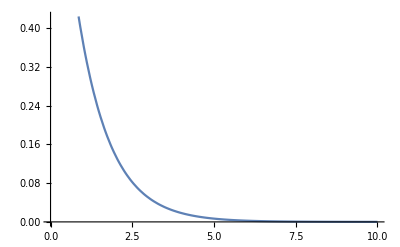

```mathematica
Plot[n1[t],{t1,0,10}]
```

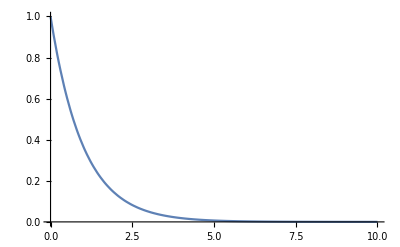

```mathematica
Plot[n1[t],{t1,0,10},PlotRange->{0,1}]
```

End :)